# Voronoi Gene - Drive Art

## Generate

## Generate Points and Create Mesh

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/Dev/HectorSanchez/VoroniArt

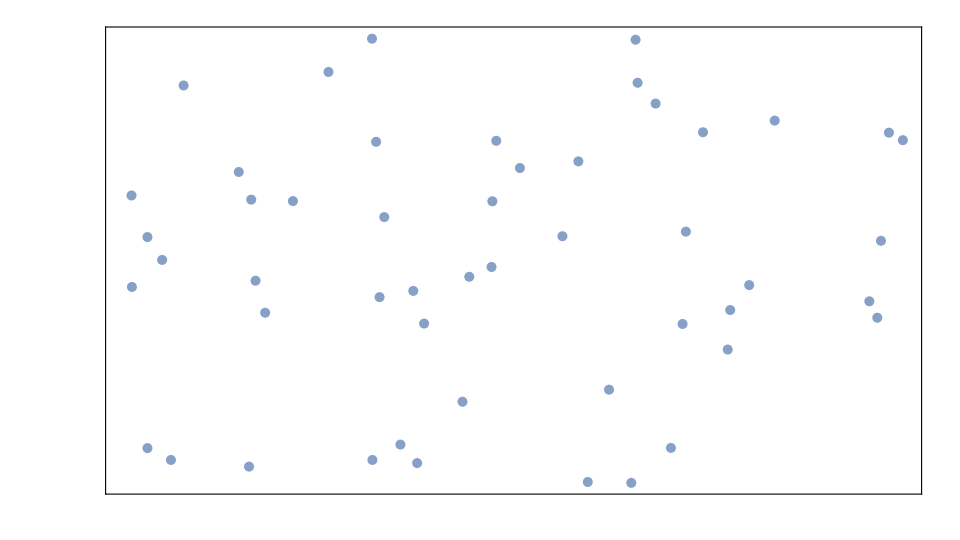

./GeoVoronoi/xySeeds.csv

./GeoVoronoi/xyEuclidean.csv

```mathematica
SetDirectory[NotebookDirectory[]]
{points,imageSize}={100,{3840,2160}};
xyPoints=Transpose[RandomInteger[{0,#},Round[points/2]]&/@imageSize];
euclideanDistances=Table[N[EuclideanDistance[xyPoints[[i]],#]]&/@xyPoints,{i,1,xyPoints//Length}];
listPlotPoints=ListPlot[xyPoints
,AspectRatio->Automatic
,PlotRange->({0,#}&/@imageSize)
,Frame->True
,FrameStyle->Directive[Gray,Thick]
,FrameTicks->None
,GridLines->None
,PlotStyle->Directive[PointSize[.0075],Opacity[.75]]
,ImageSize->Round[imageSize/4]
]
Export["./GeoVoronoi/xySeeds.csv",xyPoints]
Export["./GeoVoronoi/xyEuclidean.csv",euclideanDistances]
```

## Analyze

## Generate Mesh

```mathematica
xyPoints=Import["./GeoVoronoi/xySeeds.csv"];
listPlotPoints=ListPlot[xyPoints];
mesh=VoronoiMesh[xyPoints
,PlotTheme->"Lines"
];
composite=Show[listPlotPoints,mesh];
```

## Extract Polygons

```mathematica
vml=NestList[VoronoiMesh[Mean@@@MeshPrimitives[#,2],imageSize]&,mesh,3];
polygons=MeshPrimitives[vml[[1]],2];
polygonsGraphics=Graphics[{EdgeForm[LightPurple],Opacity[0],polygons}];
Show[composite,polygonsGraphics];
```

## Plot

## Setup Populations

```mathematica
maxPop=100;
simulatedPopulations=RandomInteger[{Round[maxPop/10],maxPop},xyPoints//Length];
polygonsRaw=MeshPrimitives[Last[vml],2];
RescalePopulation[x_,maxPop_]:=Rescale[x,{0,maxPop}]//N
```

## Plot Polygons

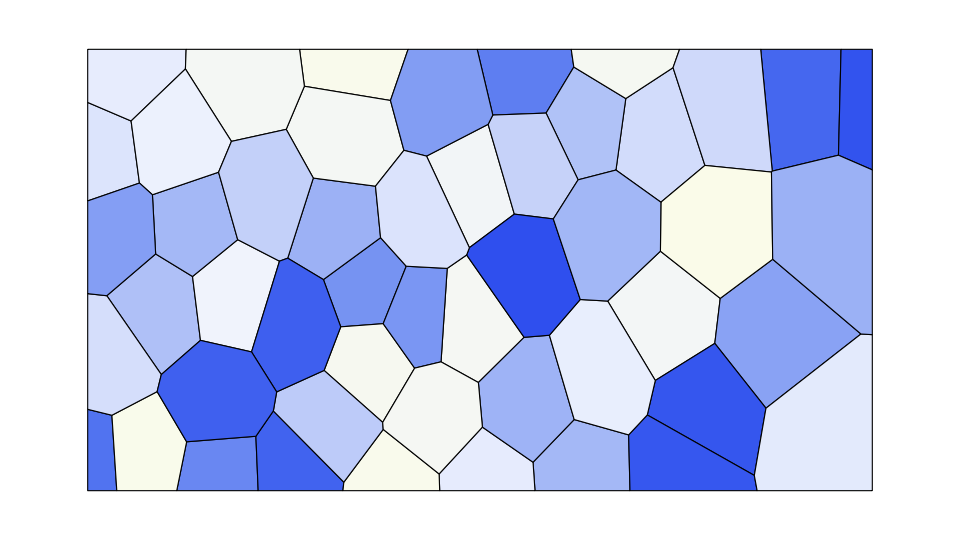

```mathematica
colorScheme=ColorData[{"TemperatureMap",{1,-1}}];
testPolygons=Table[{colorScheme[RandomReal[{0,1}]],p},{p,MeshPrimitives[Last[vml],2]}];
Graphics[{EdgeForm[Black],testPolygons}
,ImageSize->Round[imageSize/4]
]
```

## Plot Populations

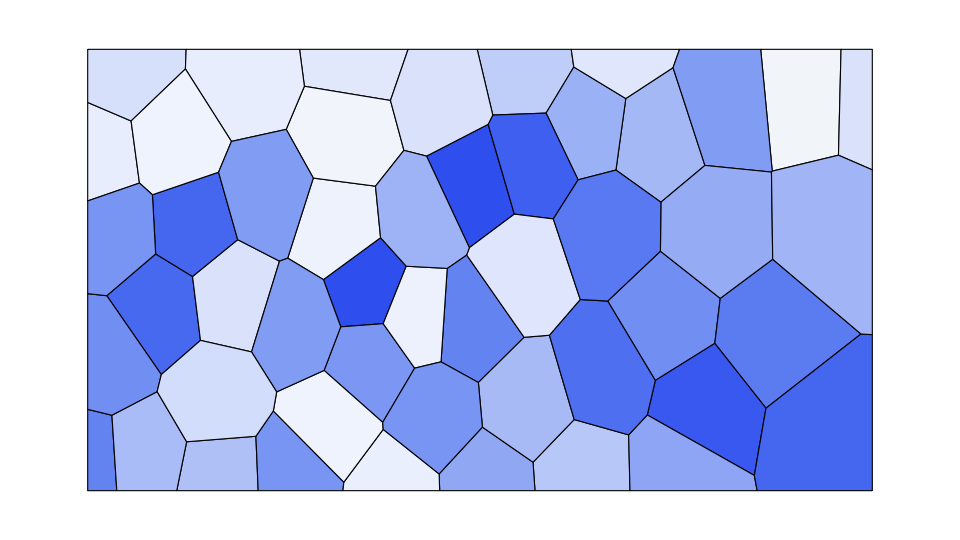

```mathematica
rescaledPopulations=RescalePopulation[simulatedPopulations,maxPop];
rescaledColors=colorScheme[#]&/@rescaledPopulations;
(*Generate Frame*)
testPolygons=Table[
{rescaledColors[[i]],polygonsRaw[[i]]}
,{i,1,polygonsRaw//Length}];
Graphics[
{EdgeForm[Black],testPolygons}
,ImageSize->Round[imageSize/4]
]
```